```mathematica
Clear[y];
```

```mathematica
f[x_,y_]:=x*Sin[x*y]
```

1

0.1

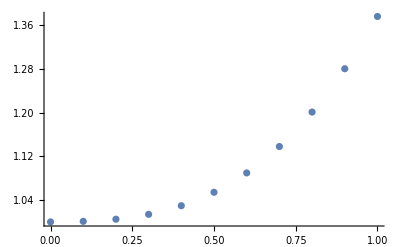

```mathematica
y[0]=1
h=.1
Do[y[n]=y[n-1]+h*f[(n-1)*h,y[n-1]],{n,1,10}]
a=ListPlot[Table[{n*h,y[n]},{n,0,10}]]
```

```mathematica
N[y[10]]
```

1.37656

```mathematica
Clear[y];
```

```mathematica
s=NDSolve[{y'[x]==x*Sin[x*y[x]],y[0]==1},y,{x,0,1}]
```

{{y→InterpolatingFunction[{{0., 1.}}, <>]}}

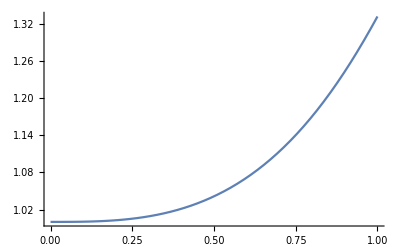

```mathematica
b=Plot[Evaluate[y[x]/.s],{x,0,1},PlotRange->All]
```

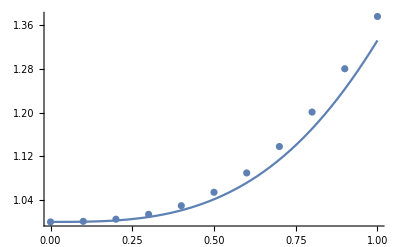

```mathematica
Show[a,b]
```

```mathematica
y[1]/.s
```

{1.33262}